```mathematica
deploy
```

CloudObject[]

# Rotations

CloudObject[]

## Util

```mathematica
(* Change TensorProduct to act like Kronecker product *)
Unprotect[TensorProduct];
TensorProduct=KroneckerProduct;
Protect[TensorProduct];

On[Assert];

(* column vectorize, following Magnus, 1999 *)
vec[W_]:=Transpose@{Flatten@Transpose[W]};
unvec[Wf_, rows_]:=Transpose[Flatten/@Partition[Wf,rows]];
toscalar[v_]:=Block[{t},
t=Flatten@v;
Assert[Length[t]==1, "scalar assert"];
First@t
];

v2c[c_]:=Transpose[{c}] (* turns vector to column matrix *)
v2r[c_]:={c} (* turns vector to row matrix *)
c2v[c_]:=Flatten[c] (* turns column matrix into vector *)

(* Partitions matrix into blocks {{axa,axb},{bxa,bxb}} *)
partitionMatrix[mat_,{a_,b_}]:=Module[{},
Assert[a+b==Length@mat];
Assert;[a+b==Length@matᵀ];
Internal`PartitionRagged[mat,{{a,b},{a,b}}]
];

(* Commutation matrix m,n *)
Kmat[m_,n_]:=Module[{x,X,before,after,positions,matrix},
X=Array[x,{m,n}];
before=Flatten@vec@X;
after=Flatten@vec@Transpose[X];
positions=MapIndexed[{First@#2,First@Flatten@Position[before,#]}&,after];
matrix=SparseArray[#->1&/@positions]
];

take1[x_]:=First@Flatten@x;

robustMin[x_]:=Min[Select[Flatten@x,#>1*^-10&]];

(* Symmetric square root *)
symsqrt[m_]:=Module[{U,S,W},
{U,S,W}=SingularValueDecomposition[m];
U.Sqrt[S].Transpose[W]
];

(* divide object by sum of its elements *)
normalize[x_]:=x/Total[x, 10];

(* Random uniform vector normalized to 1 *)
randomD[f_]:=Module[{temp},
temp=RandomReal[{0,1},{f}];
temp/Total[temp]
];

(* centers data where batch dimension is 1 *)
centerData[X_]:=Module[{Xc},
Xc=Mean@Transpose@X;
Transpose[#-Xc&/@Transpose[X]]
];

khatriRao[A_,B_]:=MapThread[Flatten[{#1}⊗{#2}]&,Transpose/@{A,B}]//Transpose

(* takes sizes [s1,s2,..] partitions vec into those sizes *)
listPartition[list_,sizes_]:=Module[{offsets,offsetPairs},
Assert[Length@list==Total@sizes, "can't partition"];
offsets={0}~Join~FoldList[Plus,sizes];
offsetPairs=Partition[offsets,2,1];
list[[#[[1]]+1;;#[[2]]]]&/@offsetPairs
];
Assert[listPartition[{1,2,3,4,5},{3,2}]=={{1,2,3},{4,5}}];

(* approximate equality testing *)
DotEqual[a_,b_]:=Norm[Flatten[{a}]-Flatten[{b}],∞]<1*^-9;

Unprotect[toc];
toc[nb_]:=Button[Mouseover[#,Style[#,"HyperlinkActive"]]&@First@NotebookRead@#,SelectionMove[#,All,CellContents],Appearance->None,BaseStyle->"Hyperlink",Alignment->Left,ImageSize->100]&/@Cells[CellStyle->{"Title","Chapter","Section","Subsection","Subsubsection"}]//CreatePalette[Panel[Column[#,Dividers->Center],ImageSize->100],FrontEnd`ClosingSaveDialog->False,WindowTitle->"Table of Contents",Magnification->1.5]&;
toc[Optional[Automatic,Automatic]]:=nbTOC@EvaluationNotebook[]
Protect[toc];


(* Things more specific to natural gradient stuff *)

(* partitions matrix into blocks *)
partitionMatrix[mat_,sizes_]:=Module[{},
Internal`PartitionRagged[mat,{sizes,sizes}]
];

(* extracts i,j'th block, taking sizes from fsizes *)
(* TODO: generalize fs *)
matrixBlock[i_,j_,mat_]:=(
msizes=Times@@@(Partition[fs,2,1]//Rest);
partitionMatrix[mat,msizes][[i,j]]
);

(* extracts i'th block from vector *)
vectorBlock[i_,vec_]:=Module[{msize},
msizes=Times@@@(Partition[fs,2,1]//Rest);
listPartition[vec,msizes][[i]]
];


(* converts bool to 0,1 *)
fromBool[x_]:=If[x,1,0]
SetAttributes[fromBool, Listable]

flatten[Ws_]:=c2v[vec/@Ws];
unflatten[Wf_]:=Module[{flatVars,sizes},
sizes=Rest[Times@@#&/@Partition[fs,2,1]];
flatVars=listPartition[Wf,sizes];
Table[unvec[flatVars[[i]],fs[[i+2]]],{i,1,Length@sizes}]
];


(* creates column of ones *)
onesCol[n_]:=v2c@Table[1,{i,n}];
onesRow[n_]:=v2r@Table[1,{i,n}];

(* Identity matrix truncated to fit rectangular dims *)
truncatedIdentity[a_,b_]:=Module[{mat},
mat=IdentityMatrix[Max[a,b]];
mat[[;;a,;;b]]
];

(* Deploys current notebook, returns URL object *)
deploy:=Module[{result},
result=CloudDeploy[SelectedNotebook[],Permissions->"Public"];
CopyToClipboard[result⟦1⟧];
result
];


(* Generate correlated data in many dimensions *)
generateX[n_,e_,dsize_]:=Module[{wt,mean,cov,normal,X},
mean=Table[0,{n}];
cov=IdentityMatrix[n]*e+Array[1-e&,{n,n}];
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
centerData[X]
];

(* Takes table of matrix blocks, inverts diagonal ones *)
blockDiagonalInverse[blocks_]:=Module[{invertMaybe},
invertMaybe[block_,{i_,j_}]:=
If[i==j,PseudoInverse@block,Array[0&,Dimensions[block]]];
MapIndexed[invertMaybe,blocks,{2}]];
```

SetDelayed::write: Tag flatten in flatten[Ws_] is Protected.

SetDelayed::write: Tag unflatten in unflatten[Wf_] is Protected.

## Equation setup

```mathematica
(* Convention, equations end with "Eq", functions end with capital F. Filenames all lowercase and separated with _.
Own symbols start with lower letter.

Globals:
lossEq: equation for loss
errEq: equation for error
gradEq: equation for gradient
hessEq: equation for Hessian
pre0: dummy preconditioner
n: number of layers
dsize: number of datapoints, aka f[-1]
fs: list of sizes
f[i]: gives dims, f[i],f[i-1] is dimension of layer i
W[i,j]: W[i].W[i-1]..W[j]
U[i,j]: U[i].U[i+1]...U[j]
makeW[i]: creates matrix of form {{W[i][1,1],W[i][1,2],...
Y: contains array of outputs
vars: contains all W's except W0 (same as X)
allvars: contains all W's
A[i],B[i],B[i].A[i]ᵀ define activation, backprop, gradient for layer i
Bn[i] truncated backprop for Newton's method
hessBlock[i,j] gives Hessian of layer i with respect to layer j
hess[i,j] gives Mathematica derived Hessian of layer i with respect to layer j
gradBlock[i] gives gradient at layer i
grad[i]: gives Mathematica gradient of layer i
sub1: replaces all W's and Y's with 1's
subr: replaces all W's and Y's with fixed random-looking number
*)

(* Number of features per layer *)
(* Number of layers, aka number of matmuls *)
(* f[i] shorthand for shape, W[i] has dimensions f[i]xf[i-1] *)
(* f[-1] is shorthand for dsize *)
Unprotect[lossEq,errEq,gradEq,hessEq,errF,lossF,gradF,hessF,pre0,n,dsize,W,U,makeW,Y,X,vars,Wf,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];
Clear[lossEq,errEq,gradEq,hessEq,n,dsize,W,U,makeW,Y,X,vars,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];

fs={10,2,2,2};
n=Length[fs]-2;
Block[{i},For[i=1, i≤Length[fs],i++,f[i-2]=fs[[i]]]];
dsize=f[-1];

(* TODO: seal flatten/unflatten *)
Unprotect[flatten,unflatten];
flatten[Ws_]:=c2v[vec/@Ws];
unflatten[Wf_]:=Module[{flatVars,sizes},
sizes=Rest[Times@@#&/@Partition[fs,2,1]];
flatVars=listPartition[Wf,sizes];
Table[unvec[flatVars[[i]],fs[[i+2]]],{i,1,Length@sizes}]
];
Protect[flatten,unflatten];

makeW[k_]:=Array[W[k],{f[k],f[k-1]}];
vars=Table[makeW[k],{k,1,n}]; (* W1, W2, ..., Wn *)
Wf=flatten@vars;
allvars=Table[makeW[k],{k,0,n}]; (* W0, W1, W2, ..., Wn *)

Y=Array[y,{f[n],f[-1]}];
X=makeW[0];

errEq=Y-Fold[Dot,Reverse@allvars];
lossEq=1/2Tr[errEqᵀ.errEq]/dsize;
gradEq=D[lossEq,{Wf,1}];
hessEq=D[lossEq,{Wf,2}];
pre0=IdentityMatrix[Length@Wf];

(* Partial products. Shorthand notation for doing product of all layers between j and i (inclusive). W refers to original sums and U is transpose *)

(* W[i,j]=W[j].W[j-1]...W[i] *)
W[bottom_,top_]:=IdentityMatrix[f[bottom]]/;bottom<top;
W[bottom_,top_]:=Module[{sublist},
Assert[top≤bottom,"W ordering"];
sublist=allvars[[top+1;;bottom+1]];
Fold[Dot,Reverse@sublist]
];

(* U[i,j]=U[i].U[i+1]...U[j] *)
U[bottom_,top_]:=IdentityMatrix[f[top]]/;bottom>top
U[bottom_,top_]:=Module[{sublist},
Assert[bottom≤top,"U ordering"];
sublist=Transpose/@allvars[[bottom+1;;top+1]];
Fold[Dot,sublist]
];

(* Activation at layer i. Defines derivative for layer i. A[0]=Identit[dsize] *)
A[i_]:=W[i-1,0];          

(* Backprop at layer i. Defines derivative for layer i. B[n]=d_error *)
B[i_]:=-U[i+1,n].errEq/dsize;

(* Partial products needed for Newton's method *)
Bn[i_]:=U[i+1,n];

hessBlock[i_,j_]:=Module[{term1,term2},
term1=(A[i].A[j]ᵀ)⊗(Bn[i].Bn[j]ᵀ)/dsize;
Assert[Dimensions@term1=={f[i]*f[i-1],f[j]*f[j-1]}];
term2=Which[
i==j,Array[0&,Dimensions[term1]],
i<j,(A[i].B[j]ᵀ)⊗U[i+1,j-1],
i>j,U[j+1,i-1]ᵀ⊗(B[i].A[j]ᵀ)
];
(term1+term2.Kmat[f[j],f[j-1]])
];

gradBlock[i_]:=c2v@vec[B[i].A[i]ᵀ];

(* substitutes 1 to every variable *)
sub1:=Module[{},
everything=Flatten[vec/@allvars]~Join~c2v@vec@Y;
Thread[everything->Array[1&,Length@everything]]
];

(* substitutes random value to every variable *)
subr:=Module[{},
SeedRandom[0];
everything=Flatten[vec/@allvars]~Join~c2v@vec@Y;
Thread[everything->RandomReal[{-1,1},Length@everything]]
];

(* Functional versions of equations *)
errF[W_]:=errEq/.subX/.subY/.subW[W];
lossF[W_]:=lossEq/.subX/.subY/.subW[W];
gradF[W_]:=gradEq/.subX/.subY/.subW[W];
hessF[W_]:=hessEq/.subX/.subY/.subW[W];

(* Run checks *)
grad[i_]:=Module[{},Assert[i≥0 && i≤n,"grad i check"];
D[lossEq,{c2v@vec@allvars[[i+1]],1}]];

hess[i_,j_]:=Module[{},Assert[j≥0&&j≤n,"hess j check"];
D[grad[i],{c2v@vec@allvars[[j+1]],1}]];

Protect[lossEq,errEq,gradEq,hessEq,errF,lossF,gradF,hessF,pre0,n,dsize,W,U,makeW,Y,X,vars,Wf,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];

idx=Range[n+1]-1; (* all valid layer indices, including W0 *)
blockIdx=Outer[List,idx,idx];

(* Checks correctness of block i,j *)
hessCheck[i_,j_]:=hess[i,j]≐hessBlock[i,j]/.subr;
gradCheck[i_]:=grad[i]==gradBlock[i]/.subr;
gradCheck/@idx
Apply[hessCheck, blockIdx,{2}]//MatrixForm
```

{True,True,True}

(True | True | True
True | True | True
True | True | True)

## Data setup

```mathematica
generateX[n_,e_,dsize_]:=Module[{wt,mean,cov,normal,X},
SeedRandom[0];
mean=Table[0,{n}];
cov=IdentityMatrix[n]*e+Array[1-e&,{n,n}];
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
centerData[X]
];
SeedRandom[0]
X0=generateX[f[0],0.01,dsize];
θ0=Pi/20;
Y0=RotationMatrix[θ0].X0;
(*Export["~/git/whitening/exp/data/rotations_simple_X0.csv",X0];*)
(*Export["~/git/whitening/exp/data/rotations_simple_Y0.csv",Y0];*)

makeInitializer[k_]:=truncatedIdentity[f[k],f[k-1]];
W0s=Table[makeInitializer[k],{k,1,n}];
W0f=flatten@W0s;
(*Export["~/git/whitening/exp/data/rotations_simple_W0f.csv",W0f];*)
(*Export["~/git/whitening/exp/data/rotations_simple_fs.csv",fs];*)

(* Todo: refactor into helper functions *)
subX:=Thread[Flatten@X->Flatten@X0];
subY:=Thread[Flatten@Y->Flatten@Y0];
subW[Wfval_]:=(Assert[Length@Wfval==Length@Wf];Thread[Wf->Wfval]);
subW0:=subW[W0f];
```

## Optimizer setup

```mathematica
(* Applies single step of optimization *)
step[x_,lr_,pre_,grad_,lossFunc_]:=Module[{},
pointsList=pointList~Append~x;
gradList=gradList~Append~grad;
preList=preList~Append~pre;
lossList=lossList~Append~lossFunc[x];
x-lr*pre.grad
];
resetStep:=({pointList, gradList,preList, lossList}={{},{},{},{}};W0f);
```

## Optimizer experiments

### Gradient Descent

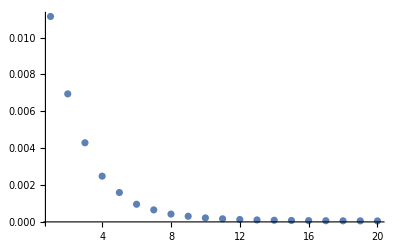

```mathematica
optimizeGradient[lr_,iters_]:=Module[{w},
w=resetStep;
For[iter=1,iter≤iters,iter++,
w=step[w,lr,pre0,gradF[w],lossF]
];
];
optimizeGradient[1.,20];
(*Export["~/git/whitening/exp/data/rotations_simple_gradient_losses.csv",lossList];*)
ListPlot[lossList,PlotRange->All]
```

```mathematica
lossList
```

{0.0111498,0.00694816,0.00429464,0.00248228,0.00159361,0.000957424,0.000651653,0.000423802,0.000306749,0.00021772,0.000167937,0.000129983,0.00010703,0.0000895942,0.0000782797,0.0000696508,0.0000636468,0.000058967,0.0000554575,0.0000526055}

### Newton's method

```mathematica
(*Export["~/git/whitening/exp/data/rotations_simple_newton_hess0.csv",hessF[W0f]];*)
(*Export["~/git/whitening/exp/data/rotations_simple_newton_ihess0.csv",ihessF[W0f]];*)
```

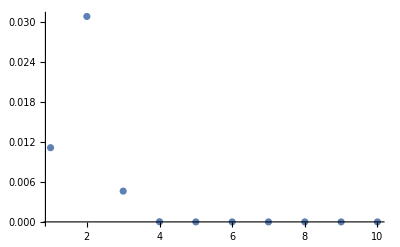

```mathematica
ihessF[W_]:=PseudoInverse@hessF@W;
optimizeNewton[lr_,iters_]:=Module[{w},
w=resetStep;
For[iter=1,iter≤iters,iter++,
w=step[w,lr,ihessF[w],gradF[w],lossF]
];
];
optimizeNewton[1.,10];
(*Export["~/git/whitening/exp/data/rotations_simple_newton_losses.csv",lossList];*)
ListPlot[lossList,PlotRange->All]
```

```mathematica
lossList
```

{0.0111498,0.0308658,0.00462571,0.0000251229,1.38508×10^-9,1.32383×10^-17,2.39119×10^-31,2.05575×10^-32,1.78886×10^-33,1.78886×10^-33}

### Newton' s method with own implementation

```mathematica
myHess0=Table[hessBlock[i,j],{i,1,n},{j,1,n}];
myhessF[W_]:=ArrayFlatten[myHess0]/.subX/.subY/.subW[W];
myihessF[W_]:=PseudoInverse[myhessF[W]];
ihessF[W0f]≐myihessF[W0f]
```

True

```mathematica
optimizeNewton2[lr_,iters_]:=Module[{w},
w=resetStep;
For[iter=1,iter≤iters,iter++,
w=step[w,lr,myihessF[w],gradF[w],lossF]
];
];
optimizeNewton2[1.,10];
ListPlot[lossList,PlotRange->All]
```

-Graphics-

## Block-diagonal Newton

```mathematica
myHess0=Table[hessBlock[i,j],{i,1,n},{j,1,n}];
ihessBdF[W_]:=ArrayFlatten[blockDiagonalInverse[myHess0/.subX/.subY/.subW[W]]];
```

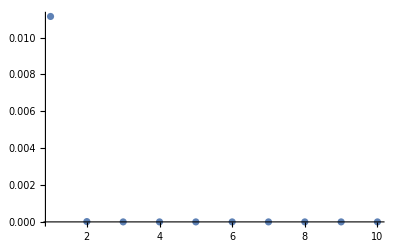

```mathematica
optimizeNewtonBd[lr_,iters_]:=Module[{w},
w=resetStep;
For[iter=1,iter≤iters,iter++,
w=step[w,lr,ihessBdF[w],gradF[w],lossF]
];
];
optimizeNewtonBd[.5,10];
Export["~/git/whitening/exp/data/rotations_simple_newtonbd_losses.csv",lossList];
ListPlot[lossList,PlotRange->All]
```